-5.00391+0.000530695 x

-6.14724+0.000500917 x

-108.55+0.00113679 x

-53.8503+0.00106898 x

-0.642248+2.53478×10^-6 x

-0.373011+1.53853×10^-6 x

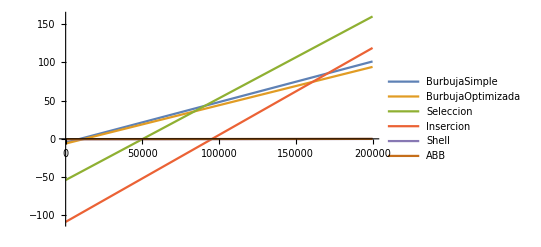

```mathematica
burbujaSimple=Fit[{{100,0.0000379085540771484375},{500,0.000477075576782226},{800,0.00108814239501953},{1000,0.00172591209411621},{1500,0.00720596313476562},{2000,0.0124430656433105},{4000,0.074679852},{6000,0.156076193},{8000,0.171564102},{10000,0.288758993},{15000,0.918097019},{20000,1.580190897},{40000,8.452590942},{60000,20.97909689},{80000,36.00872087},{90000,38.71759105},{100000,34.32539296},{120000,45.06316805},{150000,69.61539507},{200000,125.895797}},{1,x},x]

BSO=Fit[{{100,0.0000259876251220703},{500,0.000544071},{800,0.001171112},{1000,0.001971006},{1500,0.008566141},{2000,0.010462046},{4000,0.06998992},{6000,0.165845156},{8000,0.156778097},{10000,0.296716928},{15000,0.615751028},{20000,1.121236086},{40000,4.966567039},{60000,11.57947397},{80000,21.15674901},{90000,25.99217796},{100000,29.47539186},{120000,44.48436809},{150000,69.18493414},{200000,123.0501759}},{1,x},x]

Insercion=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,x},x]

seleccion=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x},x]

shell=Fit[{{100,0.0000109672546386718},{1000,0.000222921},{5000,0.001991034},{10000,0.004676819},{50000,0.035503864},{100000,0.092874},{200000,0.210251},{400000,0.514998913},{600000,0.739268064},{800000,1.197546005},{1000000,1.395174},{2000000,3.652161121},{3000000,5.442030907},{4000000,8.388068914},{5000000,11.30365992},{6000000,13.19297218},{7000000,15.91136098},{8000000,21.30137181},{9000000,22.20038104},{10000000,26.47416902}},{1,x},x]

abb=Fit[{{100,0.0000159740447998046},{1000,0.0001719},{5000,0.001017094},{10000,0.002295017},{50000,0.015423059},{100000,0.036169},{200000,0.08591},{400000,0.249607086},{600000,0.449668169},{800000,0.649112225},{1000000,0.855236},{2000000,2.156502962},{3000000,3.60809207},{4000000,5.117367029},{5000000,6.917185783},{6000000,8.520278931},{7000000,10.20669103},{8000000,11.99638486},{9000000,13.86554408},{10000000,15.75872302}},{1,x},x]

g1=Plot[{burbujaSimple,BSO,seleccion,Insercion,shell,abb},{x,0,200000},PlotLegends->{"BurbujaSimple","BurbujaOptimizada","Seleccion","Insercion","Shell","ABB"}]
```

-0.519656+0.0001691 x+2.22402×10^-9 x^2

-0.0288546+7.55172×10^-6 x+3.03448×10^-9 x^2

-5.13494+0.0001174 x+6.03912×10^-10 x^2

0.933709-0.0000347738 x+1.26724×10^-9 x^2

-0.128825+1.70604×10^-6 x+9.60803×10^-14 x^2

-0.126987+1.14141×10^-6 x+4.604×10^-14 x^2

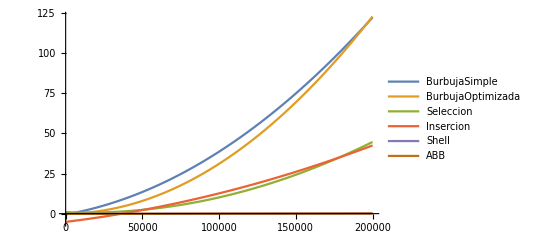

```mathematica
burbujaSimple=Fit[{{100,0.0000379085540771484375},{500,0.000477075576782226},{800,0.00108814239501953},{1000,0.00172591209411621},{1500,0.00720596313476562},{2000,0.0124430656433105},{4000,0.074679852},{6000,0.156076193},{8000,0.171564102},{10000,0.288758993},{15000,0.918097019},{20000,1.580190897},{40000,8.452590942},{60000,20.97909689},{80000,36.00872087},{90000,38.71759105},{100000,34.32539296},{120000,45.06316805},{150000,69.61539507},{200000,125.895797}},{1,x,x^2},x]

BSO=Fit[{{100,0.0000259876251220703},{500,0.000544071},{800,0.001171112},{1000,0.001971006},{1500,0.008566141},{2000,0.010462046},{4000,0.06998992},{6000,0.165845156},{8000,0.156778097},{10000,0.296716928},{15000,0.615751028},{20000,1.121236086},{40000,4.966567039},{60000,11.57947397},{80000,21.15674901},{90000,25.99217796},{100000,29.47539186},{120000,44.48436809},{150000,69.18493414},{200000,123.0501759}},{1,x,x^2},x]

Insercion=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,x,x^2},x]

seleccion=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x,x^2},x]

shell=Fit[{{100,0.0000109672546386718},{1000,0.000222921},{5000,0.001991034},{10000,0.004676819},{50000,0.035503864},{100000,0.092874},{200000,0.210251},{400000,0.514998913},{600000,0.739268064},{800000,1.197546005},{1000000,1.395174},{2000000,3.652161121},{3000000,5.442030907},{4000000,8.388068914},{5000000,11.30365992},{6000000,13.19297218},{7000000,15.91136098},{8000000,21.30137181},{9000000,22.20038104},{10000000,26.47416902}},{1,x,x^2},x]

abb=Fit[{{100,0.0000159740447998046},{1000,0.0001719},{5000,0.001017094},{10000,0.002295017},{50000,0.015423059},{100000,0.036169},{200000,0.08591},{400000,0.249607086},{600000,0.449668169},{800000,0.649112225},{1000000,0.855236},{2000000,2.156502962},{3000000,3.60809207},{4000000,5.117367029},{5000000,6.917185783},{6000000,8.520278931},{7000000,10.20669103},{8000000,11.99638486},{9000000,13.86554408},{10000000,15.75872302}},{1,x,x^2},x]

g1=Plot[{burbujaSimple,BSO,seleccion,Insercion,shell,abb},{x,0,200000},PlotLegends->{"BurbujaSimple","BurbujaOptimizada","Seleccion","Insercion","Shell","ABB"}]
```

-1.67871+0.000378947 x-9.51029×10^-10 x^2+1.11022×10^-14 x^3

-0.0998419+0.000020404 x+2.84002×10^-9 x^2+6.79964×10^-16 x^3

-1.40767+0.0000152309 x+7.89524×10^-10 x^2-6.82285×10^-17 x^3

1.46243-0.0000567496 x+1.33337×10^-9 x^2-4.6366×10^-17 x^3

-0.0519355+1.42946×10^-6 x+1.78285×10^-13 x^2-5.77542×10^-21 x^3

-0.0615581+9.06049×10^-7 x+1.15993×10^-13 x^2-4.91464×10^-21 x^3

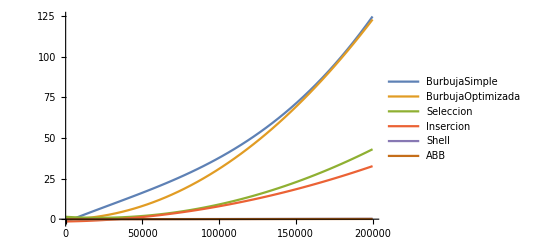

```mathematica
burbujaSimple=Fit[{{100,0.0000379085540771484375},{500,0.000477075576782226},{800,0.00108814239501953},{1000,0.00172591209411621},{1500,0.00720596313476562},{2000,0.0124430656433105},{4000,0.074679852},{6000,0.156076193},{8000,0.171564102},{10000,0.288758993},{15000,0.918097019},{20000,1.580190897},{40000,8.452590942},{60000,20.97909689},{80000,36.00872087},{90000,38.71759105},{100000,34.32539296},{120000,45.06316805},{150000,69.61539507},{200000,125.895797}},{1,x,x^2,x^3},x]

BSO=Fit[{{100,0.0000259876251220703},{500,0.000544071},{800,0.001171112},{1000,0.001971006},{1500,0.008566141},{2000,0.010462046},{4000,0.06998992},{6000,0.165845156},{8000,0.156778097},{10000,0.296716928},{15000,0.615751028},{20000,1.121236086},{40000,4.966567039},{60000,11.57947397},{80000,21.15674901},{90000,25.99217796},{100000,29.47539186},{120000,44.48436809},{150000,69.18493414},{200000,123.0501759}},{1,x,x^2,x^3},x]

Insercion=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,x,x^2,x^3},x]

seleccion=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x,x^2,x^3},x]

shell=Fit[{{100,0.0000109672546386718},{1000,0.000222921},{5000,0.001991034},{10000,0.004676819},{50000,0.035503864},{100000,0.092874},{200000,0.210251},{400000,0.514998913},{600000,0.739268064},{800000,1.197546005},{1000000,1.395174},{2000000,3.652161121},{3000000,5.442030907},{4000000,8.388068914},{5000000,11.30365992},{6000000,13.19297218},{7000000,15.91136098},{8000000,21.30137181},{9000000,22.20038104},{10000000,26.47416902}},{1,x,x^2,x^3},x]

abb=Fit[{{100,0.0000159740447998046},{1000,0.0001719},{5000,0.001017094},{10000,0.002295017},{50000,0.015423059},{100000,0.036169},{200000,0.08591},{400000,0.249607086},{600000,0.449668169},{800000,0.649112225},{1000000,0.855236},{2000000,2.156502962},{3000000,3.60809207},{4000000,5.117367029},{5000000,6.917185783},{6000000,8.520278931},{7000000,10.20669103},{8000000,11.99638486},{9000000,13.86554408},{10000000,15.75872302}},{1,x,x^2,x^3},x]

g1=Plot[{burbujaSimple,BSO,seleccion,Insercion,shell,abb},{x,0,200000},PlotLegends->{"BurbujaSimple","BurbujaOptimizada","Seleccion","Insercion","Shell","ABB"}]
```

-0.141273-0.0000406877 x+1.08914×10^-8 x^2-9.16426×10^-14 x^3+2.70052×10^-19 x^4

-0.0214544-9.91421×10^-7 x+3.44382×10^-9 x^2-4.55857×10^-15 x^3+1.37689×10^-20 x^4

7.34056-0.000400925 x+2.35585×10^-9 x^2-1.76108×10^-15 x^3+5.06409×10^-22 x^4

-3.14247+0.000234829 x-3.72062×10^-10 x^2+2.91292×10^-15 x^3-1.55504×10^-21 x^4

-0.0400139+1.35877×10^-6 x+2.17949×10^-13 x^2-1.24843×10^-20 x^3+3.46719×10^-28 x^4

-0.0222793+6.73151×10^-7 x+2.46674×10^-13 x^2-2.70187×10^-20 x^3+1.14236×10^-27 x^4

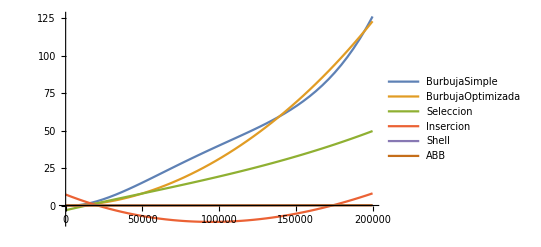

```mathematica
burbujaSimple=Fit[{{100,0.0000379085540771484375},{500,0.000477075576782226},{800,0.00108814239501953},{1000,0.00172591209411621},{1500,0.00720596313476562},{2000,0.0124430656433105},{4000,0.074679852},{6000,0.156076193},{8000,0.171564102},{10000,0.288758993},{15000,0.918097019},{20000,1.580190897},{40000,8.452590942},{60000,20.97909689},{80000,36.00872087},{90000,38.71759105},{100000,34.32539296},{120000,45.06316805},{150000,69.61539507},{200000,125.895797}},{1,x,x^2,x^3,x^4},x]

BSO=Fit[{{100,0.0000259876251220703},{500,0.000544071},{800,0.001171112},{1000,0.001971006},{1500,0.008566141},{2000,0.010462046},{4000,0.06998992},{6000,0.165845156},{8000,0.156778097},{10000,0.296716928},{15000,0.615751028},{20000,1.121236086},{40000,4.966567039},{60000,11.57947397},{80000,21.15674901},{90000,25.99217796},{100000,29.47539186},{120000,44.48436809},{150000,69.18493414},{200000,123.0501759}},{1,x,x^2,x^3,x^4},x]

Insercion=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,x,x^2,x^3,x^4},x]

seleccion=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x,x^2,x^3,x^4},x]

shell=Fit[{{100,0.0000109672546386718},{1000,0.000222921},{5000,0.001991034},{10000,0.004676819},{50000,0.035503864},{100000,0.092874},{200000,0.210251},{400000,0.514998913},{600000,0.739268064},{800000,1.197546005},{1000000,1.395174},{2000000,3.652161121},{3000000,5.442030907},{4000000,8.388068914},{5000000,11.30365992},{6000000,13.19297218},{7000000,15.91136098},{8000000,21.30137181},{9000000,22.20038104},{10000000,26.47416902}},{1,x,x^2,x^3,x^4},x]

abb=Fit[{{100,0.0000159740447998046},{1000,0.0001719},{5000,0.001017094},{10000,0.002295017},{50000,0.015423059},{100000,0.036169},{200000,0.08591},{400000,0.249607086},{600000,0.449668169},{800000,0.649112225},{1000000,0.855236},{2000000,2.156502962},{3000000,3.60809207},{4000000,5.117367029},{5000000,6.917185783},{6000000,8.520278931},{7000000,10.20669103},{8000000,11.99638486},{9000000,13.86554408},{10000000,15.75872302}},{1,x,x^2,x^3,x^4},x]

g1=Plot[{burbujaSimple,BSO,seleccion,Insercion,shell,abb},{x,0,200000},PlotLegends->{"BurbujaSimple","BurbujaOptimizada","Seleccion","Insercion","Shell","ABB"}]
```

0.516742-0.000566326 x+9.99756×10^-8 x^2-5.90874×10^-12 x^3+1.70318×10^-16 x^4-2.50739×10^-21 x^5+1.94326×10^-26 x^6-7.5416×10^-32 x^7+1.15235×10^-37 x^8

0.139882-0.000148344 x+2.83418×10^-8 x^2-1.5772×10^-12 x^3+4.54088×10^-17 x^4-6.70478×10^-22 x^5+5.24334×10^-27 x^6-2.05962×10^-32 x^7+3.18722×10^-38 x^8

0.42113-0.000104528 x+3.68568×10^-9 x^2-3.03438×10^-14 x^3+1.42669×10^-19 x^4-3.43268×10^-25 x^5+4.27728×10^-31 x^6-2.55327×10^-37 x^7+5.5625×10^-44 x^8

-1.65689+0.00041812 x-1.0197×10^-8 x^2+1.10428×10^-13 x^3-5.05429×10^-19 x^4+1.24266×10^-24 x^5-1.68957×10^-30 x^6+1.19325×10^-36 x^7-3.40375×10^-43 x^8

0.0889081-2.02157×10^-6 x+9.15851×10^-12 x^2-8.48395×10^-18 x^3+3.82072×10^-24 x^4-9.14639×10^-31 x^5+1.19178×10^-37 x^6-7.97176×10^-45 x^7+2.1411×10^-52 x^8

0.000327011+2.62645×10^-7 x+1.06888×10^-12 x^2-6.3221×10^-19 x^3+2.20885×10^-25 x^4-4.36496×10^-32 x^5+4.82736×10^-39 x^6-2.78724×10^-46 x^7+6.54442×10^-54 x^8

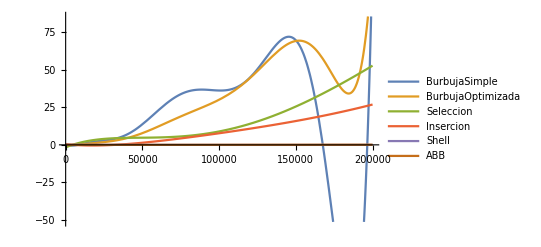

```mathematica
burbujaSimple=Fit[{{100,0.0000379085540771484375},{500,0.000477075576782226},{800,0.00108814239501953},{1000,0.00172591209411621},{1500,0.00720596313476562},{2000,0.0124430656433105},{4000,0.074679852},{6000,0.156076193},{8000,0.171564102},{10000,0.288758993},{15000,0.918097019},{20000,1.580190897},{40000,8.452590942},{60000,20.97909689},{80000,36.00872087},{90000,38.71759105},{100000,34.32539296},{120000,45.06316805},{150000,69.61539507},{200000,125.895797}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]

BSO=Fit[{{100,0.0000259876251220703},{500,0.000544071},{800,0.001171112},{1000,0.001971006},{1500,0.008566141},{2000,0.010462046},{4000,0.06998992},{6000,0.165845156},{8000,0.156778097},{10000,0.296716928},{15000,0.615751028},{20000,1.121236086},{40000,4.966567039},{60000,11.57947397},{80000,21.15674901},{90000,25.99217796},{100000,29.47539186},{120000,44.48436809},{150000,69.18493414},{200000,123.0501759}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]

Insercion=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]

seleccion=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]

shell=Fit[{{100,0.0000109672546386718},{1000,0.000222921},{5000,0.001991034},{10000,0.004676819},{50000,0.035503864},{100000,0.092874},{200000,0.210251},{400000,0.514998913},{600000,0.739268064},{800000,1.197546005},{1000000,1.395174},{2000000,3.652161121},{3000000,5.442030907},{4000000,8.388068914},{5000000,11.30365992},{6000000,13.19297218},{7000000,15.91136098},{8000000,21.30137181},{9000000,22.20038104},{10000000,26.47416902}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]

abb=Fit[{{100,0.0000159740447998046},{1000,0.0001719},{5000,0.001017094},{10000,0.002295017},{50000,0.015423059},{100000,0.036169},{200000,0.08591},{400000,0.249607086},{600000,0.449668169},{800000,0.649112225},{1000000,0.855236},{2000000,2.156502962},{3000000,3.60809207},{4000000,5.117367029},{5000000,6.917185783},{6000000,8.520278931},{7000000,10.20669103},{8000000,11.99638486},{9000000,13.86554408},{10000000,15.75872302}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]

g1=Plot[{burbujaSimple,BSO,seleccion,Insercion,shell,abb},{x,0,200000},PlotLegends->{"BurbujaSimple","BurbujaOptimizada","Seleccion","Insercion","Shell","ABB"}]
```